```mathematica
r1=(2+√5)/2
```

1/2 (2+√5)

```mathematica
r2=(2-√5)/2
```

1/2 (2-√5)

```mathematica
fp[x_]=(x-r1)(x-r2)//Expand
```

-1/4-2 x+x^2

```mathematica
f[x_]=-12Integrate[fp[x],x]+80//Expand
```

80+3 x+12 x^2-4 x^3

```mathematica
NSolve[f'[x]==0]
```

{{x→-0.118034},{x→2.11803}}

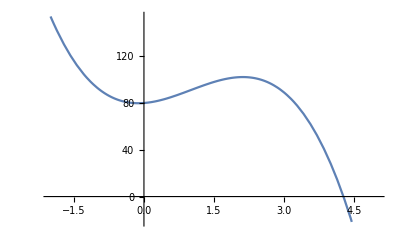

```mathematica
Plot[f[x],{x,-2,5}]
```